# Yohan Lee Lab 10

## Examples

```mathematica
f[x_]:=1/(Sqrt[x^4+x^3+1])
```

```mathematica
Function[x,1/(√(x^4+x^3+1))]
```

Function[x,1/(√(x^4+x^3+1))]

```mathematica
T3[x_]=Series[f[x],{x,0,3}]//Normal
```

1-x^3/2

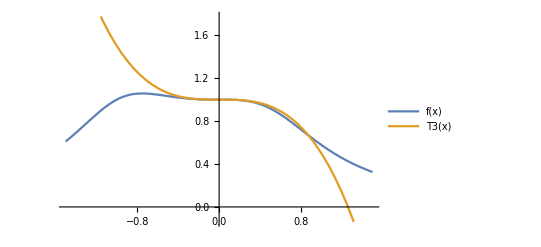

```mathematica
Plot[{f[x],T3[x]},{x,-1.5,1.5},PlotLegends->"Expressions"]
```

```mathematica
Clear[f,x]
```

```mathematica
f[x_]:=1/(Sqrt[x^4+x^3+1])
```

```mathematica
Function[x,1/(√(x^4+x^3+1))]
```

Function[x,1/(√(x^4+x^3+1))]

```mathematica
T3v2[x_]=Series[f[x],{x,1,3}]//Normal
```

1/(√3)-(7 (-1+x))/(6 √3)+(13 (-1+x)^2)/(24 √3)+(193 (-1+x)^3)/(432 √3)

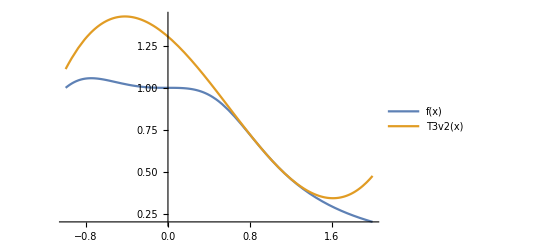

```mathematica
Plot[{f[x],T3v2[x]},{x,-1,2},PlotLegends->"Expressions"]
```

```mathematica
Clear[f,x,T3,T3v2]
```

```mathematica
f[x_]:=1/(Sqrt[x^4+x^3+1])
```

```mathematica
Function[x,1/(√(x^4+x^3+1))]
```

Function[x,1/(√(x^4+x^3+1))]

```mathematica
T3[x_]=Series[f[x],{x,-1,3}]//Normal
```

1+(1+x)/2-9/8 (1+x)^2-7/16 (1+x)^3

```mathematica
T5[x_]=Series[f[x],{x,-1,5}]//Normal
```

1+(1+x)/2-9/8 (1+x)^2-7/16 (1+x)^3+331/128 (1+x)^4+183/256 (1+x)^5

```mathematica
T7[x_]=Series[f[x],{x,-1,7}]//Normal
```

1+(1+x)/2-9/8 (1+x)^2-7/16 (1+x)^3+331/128 (1+x)^4+183/256 (1+x)^5-(6189 (1+x)^6)/1024-(2135 (1+x)^7)/2048

```mathematica
T9[x_]=Series[f[x],{x,-1,9}]//Normal
```

1+(1+x)/2-9/8 (1+x)^2-7/16 (1+x)^3+331/128 (1+x)^4+183/256 (1+x)^5-(6189 (1+x)^6)/1024-(2135 (1+x)^7)/2048+(481395 (1+x)^8)/32768+(64811 (1+x)^9)/65536

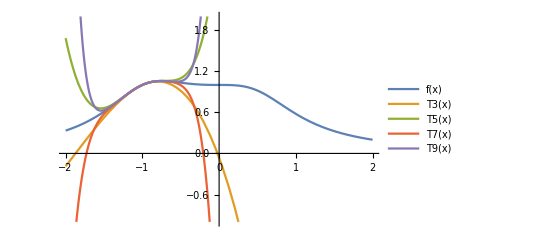

```mathematica
Plot[{f[x],T3[x],T5[x],T7[x],T9[x]},{x,-2,2},PlotLegends->"Expressions",PlotRange->{-1,2}]
```

```mathematica
Clear[f,x]
```

```mathematica
f[x_]:=x*Exp[-2x]
```

```mathematica
Function[x,x Exp[-2 x]]
```

Function[x,x Exp[-2 x]]

```mathematica
TaylorList=Table[SeriesCoefficient[f[x],{x,0,n}],{n,0,10}]
```

{0,1,-2,2,-4/3,2/3,-4/15,4/45,-8/315,2/315,-4/2835}

```mathematica
a[n_]=FindSequenceFunction[TaylorList,n]
```

((-1)^n 2^(-2+n))/Pochhammer[1,-2+n]

```mathematica
SumConvergence[a[n]x^n,n]
```

True

```mathematica
Clear[f,x,T3,T5,T7,T9]
```

```mathematica
T3[x_]=Series[Sin[x],{x,0,3}]//Normal
```

x-x^3/6

```mathematica
T3[0.3]
```

0.2955

```mathematica
Sin[c]/(4!)*(.3^4)
```

0.0003375 Sin[c]

```mathematica
Abs[Sin[0.3]-T3[0.3]]
```

0.0000202067

```mathematica
Table[{n,((Pi/4)^(n+1))/((n+1)!)},{n,4,8}]//TableForm//N
```

4. | 0.00249039
5. | 0.000325992
6. | 0.0000365762
7. | 3.59086×10^-6
8. | 3.13362×10^-7

```mathematica
T6[x_]=Series[Cos[x],{x,Pi/4,6}]//Normal
```

1/(√2)-(-π/4+x)/(√2)-(-π/4+x)^2/(2 √2)+(-π/4+x)^3/(6 √2)+(-π/4+x)^4/(24 √2)-(-π/4+x)^5/(120 √2)-(-π/4+x)^6/(720 √2)

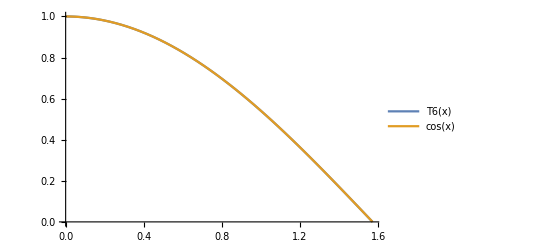

```mathematica
Plot[{T6[x],Cos[x]},{x,0,Pi/2},PlotLegends->"Expressions"]
```

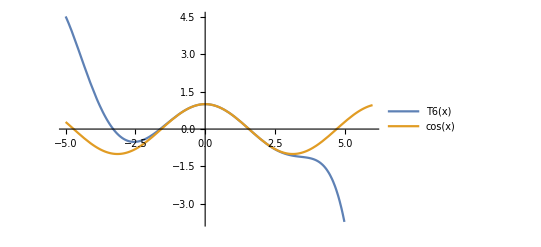

```mathematica
Plot[{T6[x],Cos[x]},{x,-5,6},PlotLegends->"Expressions"]
```

## Questions

### Q1)

```mathematica
ClearAll
```

ClearAll

```mathematica
f[x_]:=Cos[1-Exp[x]]
```

```mathematica
Function[x,Cos[1-Exp[x]]]
```

Function[x,Cos[1-Exp[x]]]

```mathematica
T5[x_]=Series[f[x],{x,1,5}]//Normal
```

Cos[1-ⅇ]+ⅇ (-1+x) Sin[1-ⅇ]+1/2 (-1+x)^2 (-ⅇ^2 Cos[1-ⅇ]+ⅇ Sin[1-ⅇ])+1/24 (-1+x)^4 (-7 ⅇ^2 Cos[1-ⅇ]+ⅇ^4 Cos[1-ⅇ]+ⅇ Sin[1-ⅇ]-6 ⅇ^3 Sin[1-ⅇ])+1/6 (-1+x)^3 (-3 ⅇ^2 Cos[1-ⅇ]+ⅇ Sin[1-ⅇ]-ⅇ^3 Sin[1-ⅇ])+1/120 (-1+x)^5 (-15 ⅇ^2 Cos[1-ⅇ]+10 ⅇ^4 Cos[1-ⅇ]+ⅇ Sin[1-ⅇ]-25 ⅇ^3 Sin[1-ⅇ]+ⅇ^5 Sin[1-ⅇ])

```mathematica
T10[x_]=Series[f[x],{x,1,10}]//Normal
```

Cos[1-ⅇ]+ⅇ (-1+x) Sin[1-ⅇ]+1/2 (-1+x)^2 (-ⅇ^2 Cos[1-ⅇ]+ⅇ Sin[1-ⅇ])+1/6 (-1+x)^3 (-3 ⅇ^2 Cos[1-ⅇ]+ⅇ Sin[1-ⅇ]-ⅇ^3 Sin[1-ⅇ])+(-1+x)^4 (-7/24 ⅇ^2 Cos[1-ⅇ]+1/24 ⅇ^4 Cos[1-ⅇ]+1/24 ⅇ Sin[1-ⅇ]-1/4 ⅇ^3 Sin[1-ⅇ])+(-1+x)^5 (-1/8 ⅇ^2 Cos[1-ⅇ]+1/12 ⅇ^4 Cos[1-ⅇ]+1/120 ⅇ Sin[1-ⅇ]-5/24 ⅇ^3 Sin[1-ⅇ]+1/120 ⅇ^5 Sin[1-ⅇ])+(-1+x)^6 (-31/720 ⅇ^2 Cos[1-ⅇ]+13/144 ⅇ^4 Cos[1-ⅇ]-1/720 ⅇ^6 Cos[1-ⅇ]+1/720 ⅇ Sin[1-ⅇ]-1/8 ⅇ^3 Sin[1-ⅇ]+1/48 ⅇ^5 Sin[1-ⅇ])+(-1+x)^8 (-(127 ⅇ^2 Cos[1-ⅇ])/40320+27/640 ⅇ^4 Cos[1-ⅇ]-(19 ⅇ^6 Cos[1-ⅇ])/2880+(ⅇ^8 Cos[1-ⅇ])/40320+(ⅇ Sin[1-ⅇ])/40320-23/960 ⅇ^3 Sin[1-ⅇ]+5/192 ⅇ^5 Sin[1-ⅇ]-(ⅇ^7 Sin[1-ⅇ])/1440)+(-1+x)^7 (-1/80 ⅇ^2 Cos[1-ⅇ]+5/72 ⅇ^4 Cos[1-ⅇ]-1/240 ⅇ^6 Cos[1-ⅇ]+(ⅇ Sin[1-ⅇ])/5040-43/720 ⅇ^3 Sin[1-ⅇ]+1/36 ⅇ^5 Sin[1-ⅇ]-(ⅇ^7 Sin[1-ⅇ])/5040)+(-1+x)^9 (-(17 ⅇ^2 Cos[1-ⅇ])/24192+(37 ⅇ^4 Cos[1-ⅇ])/1728-7/960 ⅇ^6 Cos[1-ⅇ]+(ⅇ^8 Cos[1-ⅇ])/10080+(ⅇ Sin[1-ⅇ])/362880-(605 ⅇ^3 Sin[1-ⅇ])/72576+(331 ⅇ^5 Sin[1-ⅇ])/17280-(11 ⅇ^7 Sin[1-ⅇ])/8640+(ⅇ^9 Sin[1-ⅇ])/362880)+(-1+x)^10 (-(73 ⅇ^2 Cos[1-ⅇ])/518400+(6821 ⅇ^4 Cos[1-ⅇ])/725760-(1087 ⅇ^6 Cos[1-ⅇ])/172800+(5 ⅇ^8 Cos[1-ⅇ])/24192-(ⅇ^10 Cos[1-ⅇ])/3628800+(ⅇ Sin[1-ⅇ])/3628800-(311 ⅇ^3 Sin[1-ⅇ])/120960+3/256 ⅇ^5 Sin[1-ⅇ]-(7 ⅇ^7 Sin[1-ⅇ])/4320+(ⅇ^9 Sin[1-ⅇ])/80640)

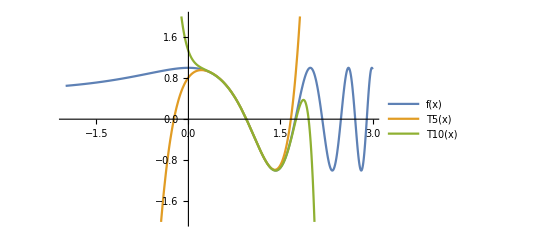

```mathematica
Plot[{f[x],T5[x],T10[x]},{x,-2,3},PlotLegends->"Expressions",PlotRange->{-2,2}]
```

### Q2)

```mathematica
ClearAll
```

ClearAll

```mathematica
f[x_]:=(1-3x)^-5
```

```mathematica
Function[x,1/(1-3 x)^5]
```

Function[x,1/(1-3 x)^5]

```mathematica
T3a[x_]=Series[f[x],{x,1/6,3}]//Normal
```

32+960 (-1/6+x)+17280 (-1/6+x)^2+241920 (-1/6+x)^3

```mathematica
T3b[x_]=Series[f[x],{x,1/2,3}]//Normal
```

-32+960 (-1/2+x)-17280 (-1/2+x)^2+241920 (-1/2+x)^3

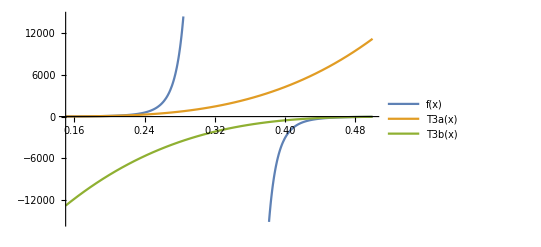

```mathematica
Plot[{f[x],T3a[x],T3b[x]},{x,0.15,0.5},PlotLegends->"Expressions"]
```

```mathematica
TaylorList=Table[SeriesCoefficient[f[x],{x,0,n}],{n,0,10}]
```

{1,15,135,945,5670,30618,153090,721710,3247695,14073345,59108049}

```mathematica
a[n_]=FindSequenceFunction[TaylorList,n]
```

1/8 3^(-2+n) n (1+n) (2+n) (3+n)

```mathematica
SumConvergence[a[n](x-1/6)^n,n]
```

Abs[-1/2+3 x]<1

```mathematica
SumConvergence[a[n](x-1/2)^n,n]
```

Abs[-3/2+3 x]<1

### Q3)

```mathematica
ClearAll
```

ClearAll

```mathematica
f[x_]:=Exp[x]
```

```mathematica
Function[x,Exp[x]]
```

Function[x,Exp[x]]

```mathematica
T3[x_]=Series[Exp[x],{x,0,3}]//Normal
```

1+x+x^2/2+x^3/6

```mathematica
T4[x_]=Series[Exp[x],{x,0,4}]//Normal
```

1+x+x^2/2+x^3/6+x^4/24

```mathematica
T5[x_]=Series[Exp[x],{x,0,5}]//Normal
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120

```mathematica
T6[x_]=Series[Exp[x],{x,0,6}]//Normal
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720

```mathematica
T7[x_]=Series[Exp[x],{x,0,7}]//Normal
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040

```mathematica
T8[x_]=Series[Exp[x],{x,0,8}]//Normal
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320

```mathematica
T9[x_]=Series[Exp[x],{x,0,9}]//Normal
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880

```mathematica
T10[x_]=Series[Exp[x],{x,0,10}]//Normal
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800

```mathematica
T11[x_]=Series[Exp[x],{x,0,11}]//Normal
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+x^11/39916800

```mathematica
T12[x_]=Series[Exp[x],{x,0,12}]//Normal
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+x^11/39916800+x^12/479001600

```mathematica
T7[1]//N
```

2.71825

```mathematica
Exp[1]//N
```

2.71828

```mathematica
R7[x_]=Exp[x]/(7!)
```

ⅇ^x/5040

```mathematica
R12[x_]=Exp[x]/(12!)
```

ⅇ^x/479001600

```mathematica
Abs[Exp[1]-T7[1]]//N
```

0.0000278602